## Region Plots final

```mathematica
costC = 0.7;
```

```mathematica
lineStyle = {Thick, Gray, Dashed};
line1 = Line[{{costC, 0}, {costC, 1}}];
```

### SD alone

```mathematica
Pnn[e_] := -1-e;
```

```mathematica
Pnc[x_,e_] :=  -1(1-x)-e;
```

```mathematica
Pcn[x_] :=-1(1-x) - costC;
```

```mathematica
Pcc[x_] :=  -1(1-x)(1-x) - costC;
```

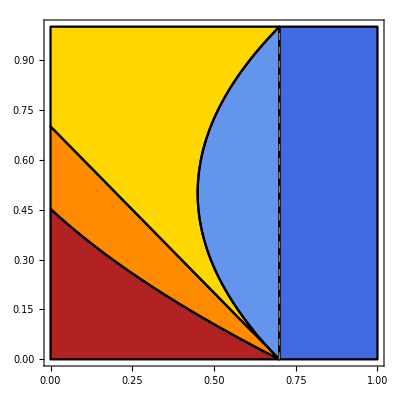

```mathematica
RegionPlot[
 {Pcc[x]>Pcn[x]>Pnc[x,e] >Pnn[e],
Pcc[x]>Pnc[x,e]>Pcn[x]>Pnn[e],
Pnc[x,e]> Pcc[x]>Pcn[x]>Pnn[e],
Pnc[x,e]> Pcc[x]>Pnn[e]>Pcn[x],
Pnc[x,e]>Pnn[e] >Pcc[x]>Pcn[x]
 } ,
{e, 0, 1}, {x, 0, 1},
FrameTicksStyle->Directive[Black, 16],
MaxRecursion -> 8,
PlotPoints -> {Automatic, {{1.6, 0}}},
(*PlotLegends -> "Expressions",*)
BoundaryStyle-> Black,
PlotStyle-> {
ColorData["HTML", "RoyalBlue"],
ColorData["HTML", "CornflowerBlue"],
ColorData["HTML", "Gold"],
ColorData["HTML", "DarkOrange"],
ColorData["HTML", "Firebrick"]},
Epilog -> {Directive[lineStyle], line1}
]
```

```mathematica
ColorData["HTML", "ColorRules"]
```

```mathematica
ColorData["HTML", "CornflowerBlue"]
```

RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824]

### SD alone + IP

```mathematica
Pnn[e_] := -1;
```

```mathematica
Pnc[x_,e_] :=  -1 (1-x)-e x;
```

```mathematica
Pcn[x_] :=-1 (1-x)-costC x;
```

```mathematica
Pcc[x_] :=  -1 (1-x)^2 -costC (1-(1-x)^2);
```

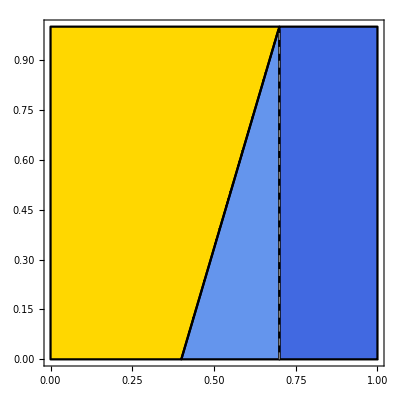

```mathematica
RegionPlot[
 {Pcc[x]>Pcn[x]>Pnc[x,e] >Pnn[e],
Pcc[x]>Pnc[x,e]>Pcn[x]>Pnn[e],
Pcc[x]>Pnc[x,e]>Pnn[e]>Pcn[x],
Pnc[x,e]> Pcc[x]>Pcn[x]>Pnn[e],
Pnc[x,e]> Pcc[x]>Pnn[e]>Pcn[x]
 } ,
{e, 0, 1}, {x, 0, 1},
FrameTicksStyle->Directive[Black, 16],
MaxRecursion -> 8,
PlotPoints -> {Automatic, {{1.6, 0}}},
(*PlotLegends -> "Expressions",*)
BoundaryStyle-> Black,
PlotStyle-> {
ColorData["HTML", "RoyalBlue"],
ColorData["HTML", "CornflowerBlue"],
ColorData["HTML", "ForestGreen"],
ColorData["HTML", "Gold"],
ColorData["HTML", "DarkOrange"]},
Epilog -> {Directive[lineStyle], line1}
]
```

### TTI alone

```mathematica
Pnn[e_] := -1-e;
```

```mathematica
Pnc[x_,e_] :=  -1(1-x)-e;
```

```mathematica
Pcn[x_] :=-1-costC;
```

```mathematica
Pcc[x_] :=  -1(1-x)-costC;
```

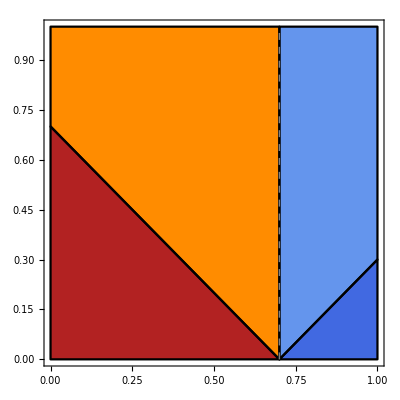

```mathematica
RegionPlot[
 { 
 
 Pcc[x]>Pcn[x]>Pnc[x,e]>Pnn[e],
 Pcc[x]>Pnc[x,e]>Pcn[x]>Pnn[e],
 Pnc[x,e]>Pcc[x]>Pnn[e]>Pcn[x],
 Pnc[x,e]>Pnn[e]>Pcc[x]>Pcn[x],

 
 } ,
{e, 0, 1}, {x, 0, 1},
FrameTicksStyle->Directive[Black, 16],
MaxRecursion -> 8,
PlotPoints -> {Automatic, {{1.6, 0}}},
(*PlotLegends -> "Expressions",*)
BoundaryStyle-> Black,
PlotStyle-> {
ColorData["HTML", "RoyalBlue"],
ColorData["HTML", "CornflowerBlue"],
ColorData["HTML", "DarkOrange"],
ColorData["HTML", "Firebrick"]},
Epilog -> {Directive[{Thick, Gray, Dashed}], line1}
]
```

### TTI alone + IP

```mathematica
Pnn[e_] := -1-e+e; (*dummy e just to have this in a function of e for Region Plot to work*)
```

```mathematica
Pnc[x_,e_] :=  -1(1-x)-e x;
```

```mathematica
Pcn[x_] :=-1-x+x; (* same trick here *)
```

```mathematica
Pcc[x_] :=  -1 (1-x)-costC x;
```

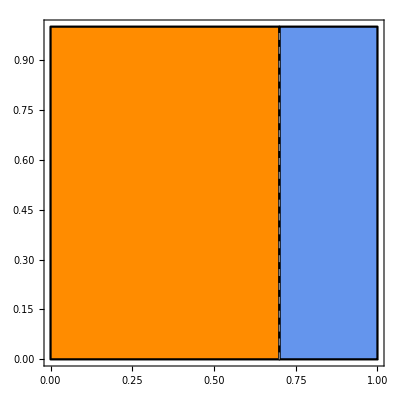

```mathematica
RegionPlot[
 { 
Pcc[x]>Pnc[x,e]>Pcn[x],
Pnc[x,e]>Pcc[x]>Pcn[x],
 } ,
{e, 0, 1}, {x, 0, 1},
FrameTicksStyle->Directive[Black, 16],
MaxRecursion -> 8,
PlotPoints -> {Automatic, {{1.6, 0}}},
(*PlotLegends -> "Expressions",*)
BoundaryStyle-> Black,
PlotStyle-> {
ColorData["HTML", "CornflowerBlue"],
ColorData["HTML", "DarkOrange"]},
Epilog -> {Directive[{Thick, Gray, Dashed}], line1}
]
```